# 「新統計入門」 小寺平治

## p.22 の例題

## データ

### 各データリストの定義

```mathematica
(*英会話*)
data22ES={55,40,75,30,50,55,70,60,45,70,20,30};
(*英文法*)
data22EG={50,49,48,42,22,19,38,30,17,56,32,17};
(*英作文*)
data22EC={35,50,55,35,45,25,50,60,35,40,25,25};
```

### 相関図のプロット

#### 英会話と英文法

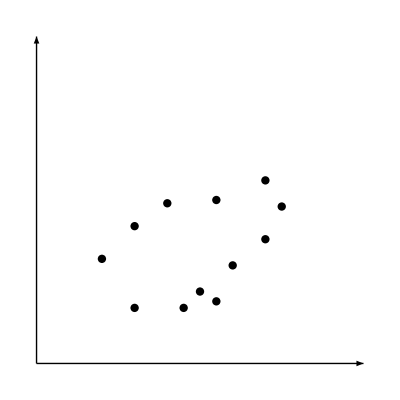

```mathematica
listESEG={};
Do[AppendTo[listESEG,{data22ES[[i]],data22EG[[i]]}],{i,1,12}];
Graphics[{
PointSize[0.015],
Point[listESEG],
Arrow[{{0,0},{100,0}}],
Arrow[{{0,0},{0,100}}]
},AspectRatio->1]
```

#### 英会話と英作文

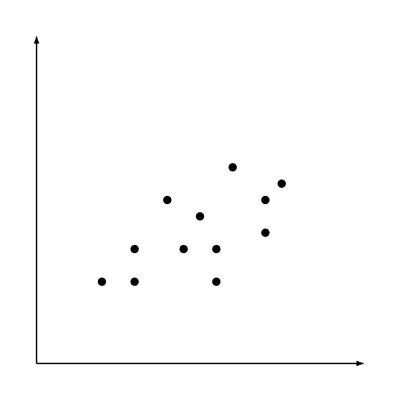

```mathematica
listESEC={};
Do[AppendTo[listESEC,{data22ES[[i]],data22EC[[i]]}],{i,1,12}];
Graphics[{
PointSize[0.015],
Point[listESEC],
Arrow[{{0,0},{100,0}}],
Arrow[{{0,0},{0,100}}]
},AspectRatio->1]
```

#### 英文法と英作文

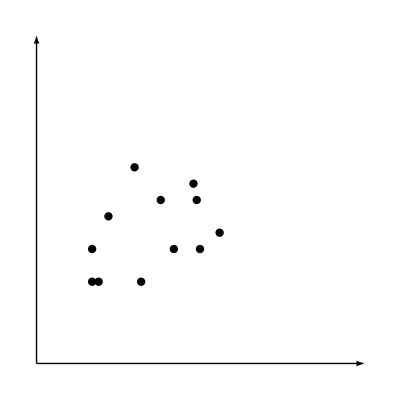

```mathematica
listEGEC={};
Do[AppendTo[listEGEC,{data22EG[[i]],data22EC[[i]]}],{i,1,12}];
Graphics[{
PointSize[0.015],
Point[listEGEC],
Arrow[{{0,0},{100,0}}],
Arrow[{{0,0},{0,100}}]
},AspectRatio->1]
```

## 代表値・散布度

### 平均

```mathematica
Mean[data22ES]
```

50

```mathematica
Mean[data22EG]
```

35

```mathematica
Mean[data22EC]
```

40

### 標準偏差

```mathematica
StandardDeviation[data22ES]
```

10 √(34/11)

```mathematica
StandardDeviation[data22EG]
```

6 √(61/11)

```mathematica
StandardDeviation[data22EC]
```

40/(√11)

### 共分散と相関係数

#### 英会話と英文法

```mathematica
Covariance[data22ES,data22EG]
```

1010/11

```mathematica
Correlation[data22ES,data22EG]
```

101/(6 √2074)

```mathematica
N[%]
```

0.369629

#### 英会話と英作文

```mathematica
Covariance[data22ES,data22EC]
```

1450/11

```mathematica
Correlation[data22ES,data22EC]
```

29/(8 √34)

```mathematica
N[%]
```

0.621682

#### 英文法と英作文

```mathematica
Covariance[data22EG,data22EC]
```

735/11

```mathematica
Correlation[data22EG,data22EC]
```

49/(16 √61)

```mathematica
N[%]
```

0.392113

## 回帰直線

### 回帰直線の定義

```mathematica
RegressionLine[list1_,list2_][x_]:=Correlation[list1,list2]*StandardDeviation[list2]/StandardDeviation[list1]*(x-Mean[list1])+Mean[list2]
```

### 散布図と回帰直線

#### 英会話と英文法

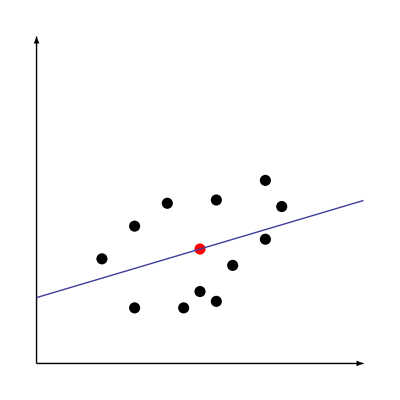

```mathematica
listESEG={};
Do[AppendTo[listESEG,{data22ES[[i]],data22EG[[i]]}],{i,1,12}];
Show[
Graphics[{
PointSize[0.02],
Point[listESEG],
Arrow[{{0,0},{100,0}}],
Arrow[{{0,0},{0,100}}],
Red,Point[{Mean[data22ES],Mean[data22EG]}]
},AspectRatio->1],
Plot[RegressionLine[data22ES,data22EG][x],{x,0,100}]
]
```

#### 英会話と英作文

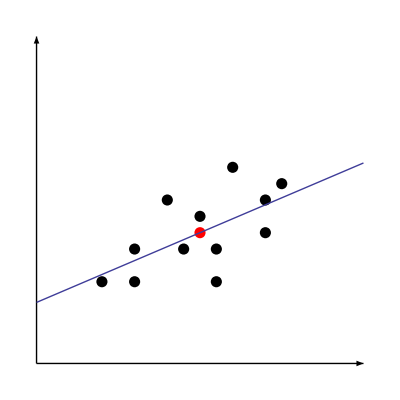

```mathematica
listESEC={};
Do[AppendTo[listESEC,{data22ES[[i]],data22EC[[i]]}],{i,1,12}];
Show[
Graphics[{
PointSize[0.02],
Point[listESEC],
Arrow[{{0,0},{100,0}}],
Arrow[{{0,0},{0,100}}],
Red,Point[{Mean[data22ES],Mean[data22EC]}]
},AspectRatio->1],
Plot[RegressionLine[data22ES,data22EC][x],{x,0,100}]
]
```

#### 英文法と英作文

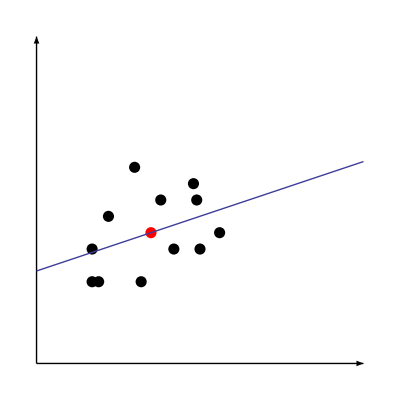

```mathematica
listEGEC={};
Do[AppendTo[listEGEC,{data22EG[[i]],data22EC[[i]]}],{i,1,12}];
Show[
Graphics[{
PointSize[0.02],
Point[listEGEC],
Arrow[{{0,0},{100,0}}],
Arrow[{{0,0},{0,100}}],
Red,Point[{Mean[data22EG],Mean[data22EC]}]
},AspectRatio->1],
Plot[RegressionLine[data22EG,data22EC][x],{x,0,100}]
]
```